## Generating universes off of cellular autonoma

Wolfram has claimed to create a Theory of Everything based off a set of fundamental rules being replicated n amount of times to generate a ruleset for said universe. Although I cannot see any physical application, I am going to attempt to make sense of the commands and see what I can make on my own.

From his “First Universe” section on his website, we use the following commands to manipulate a ruleset and “evolve” for 5 steps

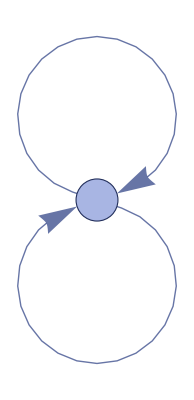
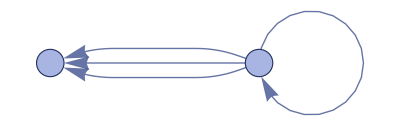
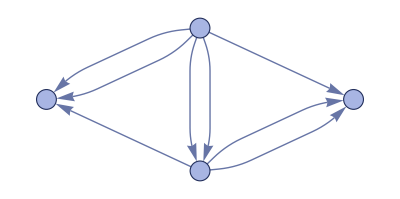
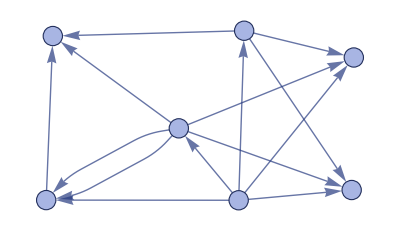
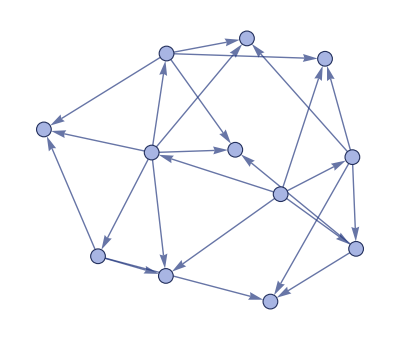
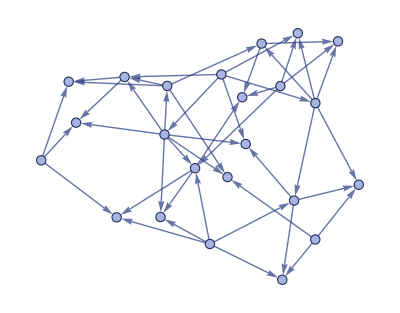

```mathematica
ResourceFunction["WolframModel"][{{x,y},{x,z}} -> {{x,z},{x,w},{y,w},{z,w}},{{0,0},{0,0}},5,"StatesPlotsList"]
```

Now I will attempt to break down the syntax so we can understand everything that is going on:

1. ResourceFunction[“WolframModel”] allows us to talk to the servers connected to mathematica to pull this function off the database and utilize its commands. Similar to import in python.
2. {{x,y},{x,z}} is our initial set of rules. Think of it as “x goes to y and x goes to z”
3. using the → relation, we have an abstract rewriting system (ARS) rule to change our rules into another set
4. Using the ARS we transition: {{x,y},{x,z}} → {{x,z},{x,w},{y,w},{z,w}}. This now reads as “x goes to z, x goes to w, y goes to w, and z goes to w”
5. We now give “starting point” initialization. {{0,0},{0,0}} is to mesh with our initial set of rules before using the ARS relation. 
6. “5” is the evolution time-step, change this for a longer cycle of evolution.
7. “StatesPlotsList” is the command to show every step in the evolution. Other command I know is “FinalStatePlot” which just shows the end result of the evolution.

Breakdown of the output:
1. {{0,0},{0,0}} are two self-loops to the 0th element.
2. {{0,0},{0,0}} were our initial x,y,z values. We now use the ARS and evolve for the first timestep. The first output includes a new variable, w, which will be element “1”. So now the first evolution is {{x,z},{x,w},{y,w},{z,w}}. With x,y,z being 0,0,0, this reads as: “0 goes to 0, 0 goes to 1, 0 goes to 1, 0 goes to 1”. This gives us the second entry, where we have 1 self loop (0 goes to 0), and 3 arrows from 0 to 1.

Below, I will post the “FinalState” values for each evolution
First evolution:

```mathematica
WolframModel[{{x,y},{x,z}}-> {{x,z},{x,w},{y,w},{z,w}},{{0,0},{0,0}},1,"FinalState"]
```

{{0,0},{0,1},{0,1},{0,1}}

Second evolution, with visual progression after:

```mathematica
WolframModel[{{x,y},{x,z}}-> {{x,z},{x,w},{y,w},{z,w}},{{0,0},{0,0}},2,"FinalState"]
```

{{0,1},{0,2},{0,2},{1,2},{0,1},{0,3},{1,3},{1,3}}

```mathematica
WolframModel[{{x,y},{x,z}}-> {{x,z},{x,w},{y,w},{z,w}},{{0,0},{0,0}},2,"StatesPlotsList"]
```

{-Graphics-,-Graphics-,-Graphics-}

You can also store this model and evolution into a variable, as shown below

```mathematica
eo = WolframModel[{{x,y},{x,z}}-> {{x,z},{x,w},{y,w},{z,w}},{{0,0},{0,0}},10]
```

WolframModelEvolutionObject[…]

This is called an evolution object, and we can do some things with this:
Displaying the final state [hidden because of size, double click cell on right hand side to expand]:

```mathematica
eo["FinalState"]
```

{{16,144},{79,147},{6,156},{24,161},{45,162},{48,163},{88,163},{25,165},{84,166},{49,167},{90,167},{89,168},{27,169},{82,169},{91,169},{92,170},{51,175},{94,175},{28,179},{52,180},{0,181},{93,182},{98,182},{23,183},{43,184},{83,184},{12,185},{55,185},{77,186},{99,188},{30,189},{101,189},{4,190},{29,191},{103,193},{57,195},{104,195},{95,197},{102,199},{107,200},{8,202},{22,204},{81,205},{60,207},{105,208},{31,210},{58,211},{61,212},{113,212},{32,214},{108,215},{62,216},{115,216},{114,217},{34,218},{106,218},{116,218},{117,219},{2,220},{86,221},{35,223},{64,224},{66,228},{121,228},{1,229},{111,230},{37,232},{67,233},{124,233},{69,237},{126,237},{10,238},{119,238},{129,244},{70,246},{132,247},{134,251},{3,253},{136,254},{20,256},{80,257},{138,257},{40,259},{127,259},{75,262},{141,262},{0,2},{0,263},{98,263},{2,263},{2,77},{2,264},{142,264},{77,264},{16,42},{16,265},{78,265},{42,265},{42,144},{42,266},{98,266},{144,266},{2,79},{2,267},{143,267},{79,267},{42,146},{42,268},{79,268},{146,268},{79,146},{79,269},{145,269},{146,269},{23,79},{23,270},{145,270},{79,270},{3,13},{3,271},{136,271},{13,271},{74,148},{74,272},{137,272},{148,272},{13,148},{13,273},{87,273},{148,273},{13,149},{13,274},{44,274},{149,274},{44,149},{44,275},{136,275},{149,275},{27,150},{27,276},{81,276},{150,276},{50,150},{50,277},{92,277},{150,277},{7,151},{7,278},{82,278},{151,278},{24,82},{24,279},{151,279},{82,279},{82,152},{82,280},{151,280},{152,280},{2,83},{2,281},{145,281},{83,281},{25,83},{25,282},{153,282},{83,282},{55,154},{55,283},{102,283},{154,283},{83,154},{83,284},{153,284},{154,284},{7,155},{7,285},{84,285},{155,285},{46,155},{46,286},{118,286},{155,286},{6,14},{6,287},{85,287},{14,287},{14,156},{14,288},{91,288},{156,288},{14,157},{14,289},{85,289},{157,289},{14,158},{14,290},{86,290},{158,290},{47,158},{47,291},{156,291},{158,291},{13,159},{13,292},{48,292},{159,292},{81,159},{81,293},{150,293},{159,293},{48,159},{48,294},{92,294},{159,294},{26,160},{26,295},{87,295},{160,295},{85,160},{85,296},{157,296},{160,296},{24,88},{24,297},{152,297},{88,297},{45,88},{45,298},{144,298},{88,298},{84,162},{84,299},{155,299},{162,299},{88,162},{88,300},{161,300},{162,300},{48,88},{48,301},{161,301},{88,301},{87,163},{87,302},{160,302},{163,302},{7,164},{7,303},{89,303},{164,303},{49,164},{49,304},{91,304},{164,304},{25,90},{25,305},{154,305},{90,305},{46,166},{46,306},{90,306},{166,306},{90,166},{90,307},{165,307},{166,307},{49,90},{49,308},{165,308},{90,308},{89,167},{89,309},{164,309},{167,309},{14,168},{14,310},{27,310},{168,310},{27,91},{27,311},{168,311},{91,311},{26,170},{26,312},{92,312},{170,312},{50,170},{50,313},{157,313},{170,313},{1,171},{1,314},{51,314},{171,314},{51,171},{51,315},{138,315},{171,315},{15,93},{15,316},{96,316},{93,316},{15,94},{15,317},{172,317},{94,317},{47,174},{47,318},{94,318},{174,318},{86,174},{86,319},{158,319},{174,319},{94,174},{94,320},{173,320},{174,320},{51,94},{51,321},{173,321},{94,321},{93,175},{93,322},{172,322},{175,322},{4,15},{4,323},{103,323},{15,323},{15,176},{15,324},{173,324},{176,324},{15,177},{15,325},{29,325},{177,325},{29,96},{29,326},{177,326},{96,326},{28,53},{28,327},{97,327},{53,327},{53,179},{53,328},{172,328},{179,328},{52,97},{52,329},{103,329},{97,329},{96,180},{96,330},{178,330},{180,330},{0,1},{0,331},{142,331},{1,331},{77,181},{77,332},{143,332},{181,332},{1,98},{1,333},{181,333},{98,333},{23,99},{23,334},{147,334},{99,334},{54,183},{54,335},{142,335},{183,335},{43,99},{43,336},{122,336},{99,336},{99,184},{99,337},{183,337},{184,337},{12,30},{12,338},{100,338},{30,338},{30,185},{30,339},{102,339},{185,339},{30,186},{30,340},{100,340},{186,340},{1,101},{1,341},{182,341},{101,341},{54,188},{54,342},{101,342},{188,342},{101,188},{101,343},{187,343},{188,343},{30,56},{30,344},{187,344},{56,344},{56,189},{56,345},{179,345},{189,345},{4,17},{4,346},{176,346},{17,346},{95,190},{95,347},{177,347},{190,347},{17,190},{17,348},{112,348},{190,348},{29,104},{29,349},{178,349},{104,349},{57,191},{57,350},{176,350},{191,350},{53,192},{53,351},{104,351},{192,351},{97,192},{97,352},{180,352},{192,352},{104,192},{104,353},{191,353},{192,353},{17,193},{17,354},{57,354},{193,354},{34,194},{34,355},{105,355},{194,355},{63,194},{63,356},{117,356},{194,356},{57,105},{57,357},{193,357},{105,357},{105,195},{105,358},{194,358},{195,358},{9,196},{9,359},{106,359},{196,359},{31,106},{31,360},{196,360},{106,360},{106,197},{106,361},{196,361},{197,361},{1,107},{1,362},{187,362},{107,362},{56,199},{56,363},{107,363},{199,363},{107,199},{107,364},{198,364},{199,364},{32,107},{32,365},{198,365},{107,365},{78,200},{78,366},{146,366},{200,366},{9,201},{9,367},{108,367},{201,367},{59,201},{59,368},{123,368},{201,368},{8,18},{8,369},{109,369},{18,369},{18,202},{18,370},{116,370},{202,370},{18,203},{18,371},{109,371},{203,371},{22,60},{22,372},{110,372},{60,372},{60,204},{60,373},{202,373},{204,373},{44,205},{44,374},{110,374},{205,374},{18,206},{18,375},{111,375},{206,375},{60,111},{60,376},{206,376},{111,376},{110,207},{110,377},{205,377},{207,377},{111,207},{111,378},{206,378},{207,378},{17,208},{17,379},{61,379},{208,379},{61,208},{61,380},{117,380},{208,380},{33,209},{33,381},{112,381},{209,381},{109,209},{109,382},{203,382},{209,382},{31,113},{31,383},{197,383},{113,383},{58,113},{58,384},{147,384},{113,384},{108,211},{108,385},{201,385},{211,385},{113,211},{113,386},{210,386},{211,386},{61,113},{61,387},{210,387},{113,387},{112,212},{112,388},{209,388},{212,388},{9,213},{9,389},{114,389},{213,389},{62,213},{62,390},{116,390},{213,390},{32,115},{32,391},{200,391},{115,391},{59,215},{59,392},{115,392},{215,392},{115,215},{115,393},{214,393},{215,393},{62,115},{62,394},{214,394},{115,394},{114,216},{114,395},{213,395},{216,395},{18,217},{18,396},{34,396},{217,396},{34,116},{34,397},{217,397},{116,397},{33,219},{33,398},{117,398},{219,398},{63,219},{63,399},{203,399},{219,399},{2,118},{2,400},{153,400},{118,400},{35,220},{35,401},{120,401},{220,401},{35,221},{35,402},{118,402},{221,402},{118,221},{118,403},{220,403},{221,403},{10,35},{10,404},{128,404},{35,404},{35,65},{35,405},{222,405},{65,405},{65,223},{65,406},{178,406},{223,406},{64,120},{64,407},{143,407},{120,407},{119,224},{119,408},{223,408},{224,408},{5,225},{5,409},{121,409},{225,409},{66,225},{66,410},{130,410},{225,410},{36,226},{36,411},{121,411},{226,411},{100,226},{100,412},{186,412},{226,412},{121,226},{121,413},{225,413},{226,413},{19,227},{19,414},{122,414},{227,414},{66,122},{66,415},{227,415},{122,415},{122,228},{122,416},{227,416},{228,416},{1,123},{1,417},{198,417},{123,417},{37,229},{37,418},{125,418},{229,418},{37,230},{37,419},{123,419},{230,419},{123,230},{123,420},{229,420},{230,420},{11,124},{11,421},{139,421},{124,421},{37,68},{37,422},{231,422},{68,422},{124,232},{124,423},{231,423},{232,423},{68,232},{68,424},{204,424},{232,424},{67,125},{67,425},{171,425},{125,425},{5,234},{5,426},{126,426},{234,426},{69,234},{69,427},{133,427},{234,427},{38,235},{38,428},{126,428},{235,428},{126,235},{126,429},{234,429},{235,429},{21,127},{21,430},{135,430},{127,430},{69,127},{69,431},{236,431},{127,431},{127,237},{127,432},{236,432},{237,432},{10,39},{10,433},{222,433},{39,433},{65,239},{65,434},{128,434},{239,434},{120,239},{120,435},{224,435},{239,435},{39,128},{39,436},{238,436},{128,436},{128,240},{128,437},{239,437},{240,437},{19,241},{19,438},{129,438},{241,438},{71,241},{71,439},{131,439},{241,439},{36,242},{36,440},{130,440},{242,440},{71,130},{71,441},{242,441},{130,441},{129,243},{129,442},{241,442},{243,442},{130,243},{130,443},{242,443},{243,443},{39,71},{39,444},{240,444},{71,444},{71,244},{71,445},{243,445},{244,445},{21,132},{21,446},{236,446},{132,446},{39,245},{39,447},{244,447},{245,447},{70,132},{70,448},{222,448},{132,448},{132,246},{132,449},{245,449},{246,449},{39,247},{39,450},{132,450},{247,450},{131,247},{131,451},{246,451},{247,451},{38,248},{38,452},{133,452},{248,452},{72,248},{72,453},{240,453},{248,453},{11,134},{11,454},{231,454},{134,454},{21,249},{21,455},{245,455},{249,455},{68,250},{68,456},{134,456},{250,456},{125,250},{125,457},{233,457},{250,457},{134,250},{134,458},{249,458},{250,458},{21,251},{21,459},{73,459},{251,459},{73,251},{73,460},{235,460},{251,460},{72,252},{72,461},{135,461},{252,461},{133,252},{133,462},{248,462},{252,462},{3,11},{3,463},{148,463},{11,463},{80,253},{80,464},{149,464},{253,464},{11,253},{11,465},{249,465},{253,465},{11,254},{11,466},{74,466},{254,466},{74,254},{74,467},{152,467},{254,467},{73,255},{73,468},{137,468},{255,468},{135,255},{135,469},{252,469},{255,469},{20,41},{20,470},{138,470},{41,470},{41,256},{41,471},{141,471},{256,471},{41,257},{41,472},{138,472},{257,472},{11,258},{11,473},{76,473},{258,473},{137,258},{137,474},{255,474},{258,474},{76,258},{76,475},{141,475},{258,475},{40,76},{40,476},{140,476},{76,476},{76,140},{76,477},{259,477},{140,477},{41,261},{41,478},{76,478},{261,478},{139,261},{139,479},{260,479},{261,479},{76,261},{76,480},{260,480},{261,480},{75,141},{75,481},{256,481},{141,481},{140,262},{140,482},{260,482},{262,482}}

Plotting the final state:

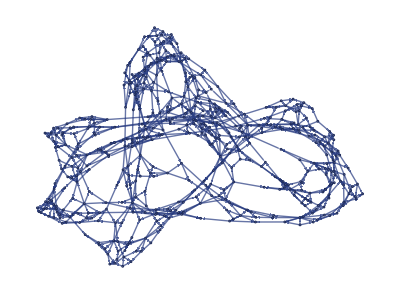

```mathematica
eo["FinalStatePlot"]
```

Displaying the vertex count list:

```mathematica
eo["VertexCountList"]
```

{1,2,4,7,12,23,42,77,142,263,483}

This means that the final plot, shown above, evolves to have 483 endpoints.

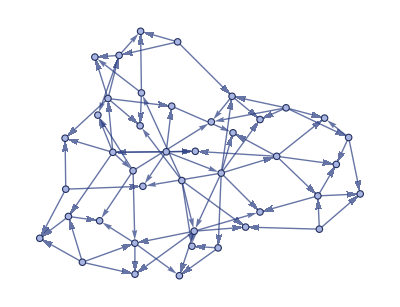
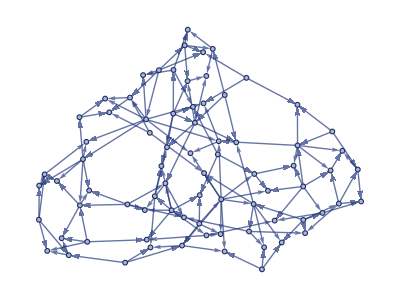
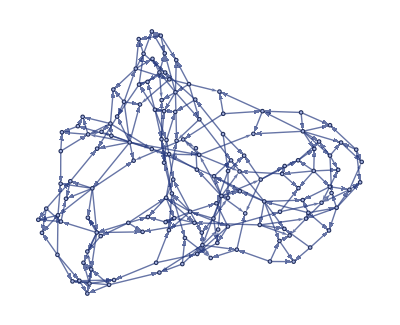
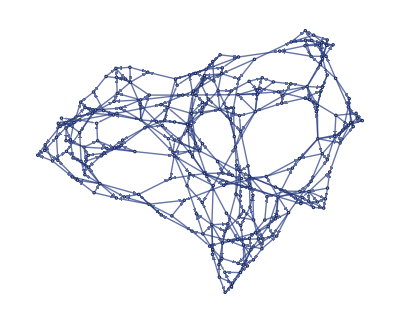
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
eo["StatesPlotsList"]
```

We can now look at the “causal graph” and the “layered causal graph”, but I have yet to know what they mean

```mathematica
eo["CausalGraph"]
```

-Graphics-

```mathematica
eo["LayeredCausalGraph",AspectRatio->1/2]
```

-Graphics-

```mathematica
wm = WolframModel
```

WolframModel

```mathematica
wm
```

WolframModel

Trying some shorthand to see if I can simplify these expressions...

```mathematica
ruleset = {{x,y},{x,z}} -> {{x,z},{x,w},{y,w},{z,w}}
```

{{x,y},{x,z}}→{{x,z},{x,w},{y,w},{z,w}}

```mathematica
initPoints = {{0,0},{0,0}}
```

{{0,0},{0,0}}

```mathematica
wm[ruleset,initPoints,5,"StatesPlotsList"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Now I am going to try a new command called “EventsStatesPlotsList”

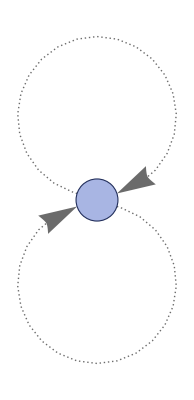
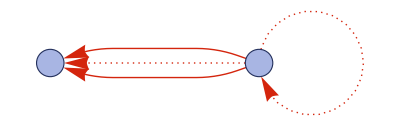
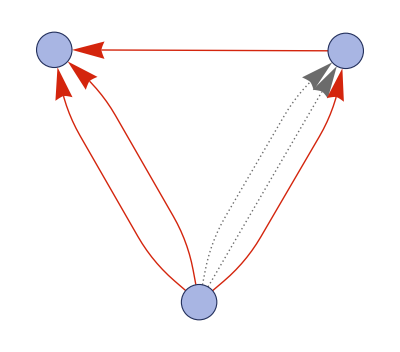
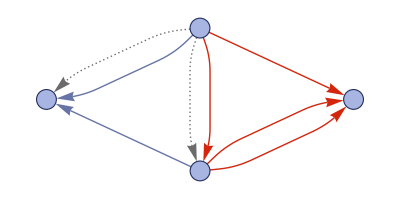
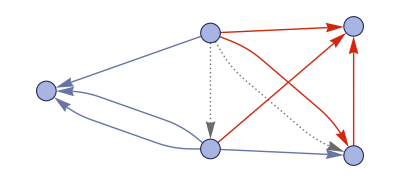
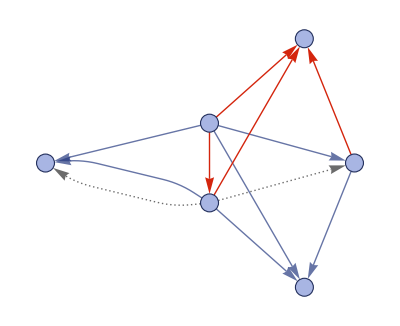
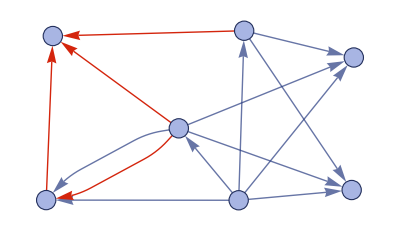

```mathematica
wm[ruleset,initPoints,3,"EventsStatesPlotsList"]
```

Compare to the states plots list:

```mathematica
wm[ruleset, initPoints, 3, "StatesPlotsList"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

It seems the events states plots list generates a list of every single action that gets us to our end result... but its hard for me to keep track of what is the end result vs what is another part of the generation... It helps that I have already seen a list of all the states before looking at the generation event.

Now I am going to try to generate this for 5 evolutions, hopefully my computer doesn’t explode haha

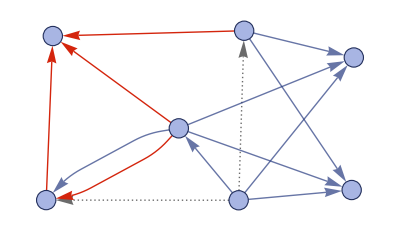
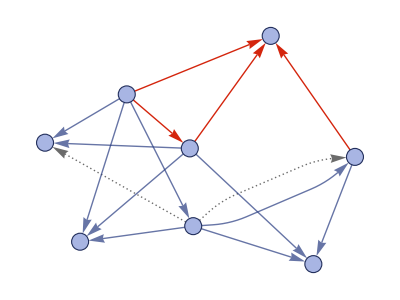
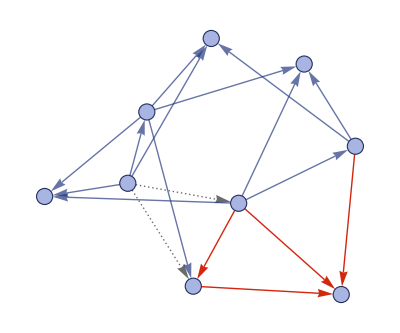
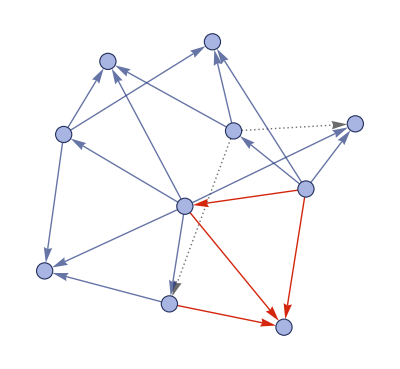
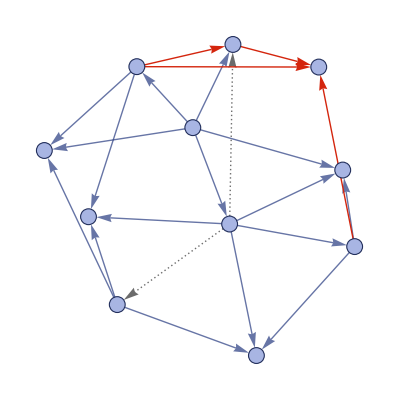
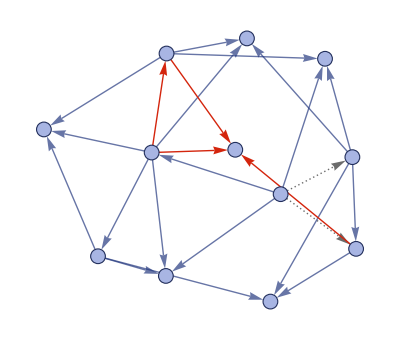
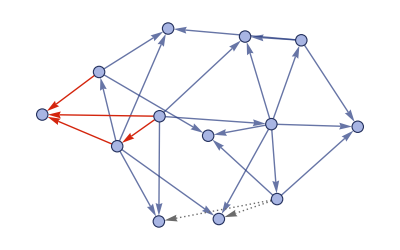
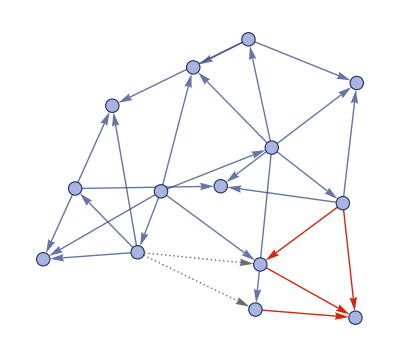
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
wm[ruleset, initPoints, 5, "EventsStatesPlotsList"]
```

Next, I am going to try looking at “Multi-way states”  [ It does not render well, but leaving the code behind to show the “proper” syntax, since it is broken on the example]

```mathematica
LayeredGraphPlot[[[ruleset],initPoints,2,"StatesGraph"], VertexSize -> 1]
```

```mathematica
LayeredGraphPlot[[[ruleset],initPoints,2,"EvolutionCausalGraph"], VertexSize -> 1]
```

## Formatting my own universe?

```mathematica
wm = ResourceFunction["WolframModel"]
```

```mathematica
ruleset = {{x,y}, {y,z}} -> {{x,x},{x,y},{y,q},{y,w},{w,z},{q,z}}
```

{{x,y},{y,z}}→{{x,x},{x,y},{y,q},{y,w},{w,z},{q,z}}

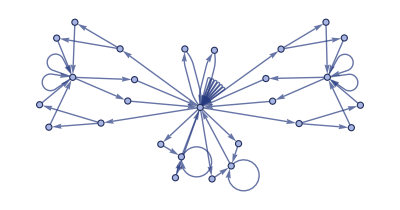
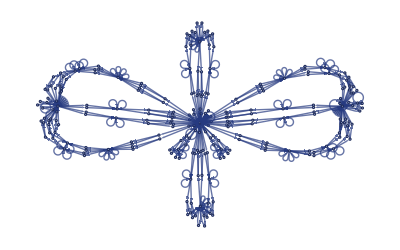
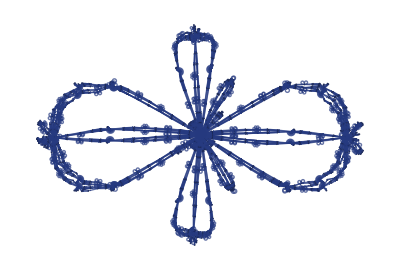
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
wm[ruleset, {{0,0},{0,0}},#,"FinalStatePlot"] &/@ {3,5,7,9}
```

```mathematica
model1 = wm[ruleset,{{0,0},{0,1}},5]
```

WolframModelEvolutionObject[…]

```mathematica
model1["VertexCountList"]
```

{2,4,10,28,82,244}

```mathematica
model1["FinalStatePlot"]
```

-Graphics-

```mathematica
model2 = wm[ruleset,{{1,0},{0,1}},5]
```

WolframModelEvolutionObject[…]

```mathematica
model2["VertexCountList"]
```

{2,4,10,28,82,244}

```mathematica
model2["FinalStatePlot"]
```

-Graphics-

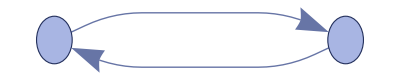
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
model2["StatesPlotsList"]
```

```mathematica
List[model1["StatesPlotsList"], model2["StatesPlotsList"]]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
List[wm[ruleset,#,5,"StatesPlotsList"]] &/@ {{{0,0},{0,0}}, {{1,1},{1,2}}, {{3,1},{1,3}}, {{1,1},{1,1}}}
```

{{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}}

## String Substitution Code

One of the things Wolfram seems to use the most is string substitution systems to "demonstrate" his point between observable states, special relativity, quantum entanglement and all that stuff .
  
  A string substitution works as such : We take some string, "A", for example, and run a set of substitutions and evolve over a time step :
   "A" -> "BBB", "BB" -> "A"
For every A, replace with BBB, then for every BB, replace with A . We will initialize at A, and run for 6 timesteps.
  This leads to the follow state graph:

```mathematica
ResourceFunction["MultiwaySystem"][{"A" -> "BBB", "BB" -> "A"}, "A", 6, "StatesGraph"]
```

-Graphics-

When we look at the events that happen between each event, Wolfram seems to consider these “commutation relations” between operators in quantum mechanics?

```mathematica
stringSub = {"A" -> "BBB", "BB" -> "A"}
```

{A→BBB,BB→A}

```mathematica
ResourceFunction["MultiwaySystem"][stringSub, "A", 6, "EvolutionEventsGraph"]
```

-Graphics-

If we want to lose the labeling and just see a structure with small node (to follow pathways), we can do the following:
For 6 iterations (as above with the evolution)

```mathematica
mws = ResourceFunction["MultiwaySystem"]
```

```mathematica
mws[stringSub, "A", 6, "EvolutionEventsGraphStructure"]
```

-Graphics-

As we can see, this renders a lot faster... Lets try 10 iterations

```mathematica
mws[stringSub, "A", 10, "EvolutionEventsGraphStructure"]
```

-Graphics-

Thats an interesting shape... Lets see what happens at 20

```mathematica
mws[stringSub, "A", 20, "EvolutionEventsGraphStructure"]
```

-Graphics-

Okay that was a weird digression, but now lets look at a causal graph for this multiway system... this is where wolfram invokes the idea of hypersurfaces and special relativity?

```mathematica
mws[stringSub, "A", 6, "CausalGraph"]
```

-Graphics-

Now we can look at the causal structure as well, without the labeling

```mathematica
mws[stringSub, "A", 6, "CausalGraphStructure"]
```

-Graphics-

Lets try 10

```mathematica
mws[stringSub, "A", 10, "CausalGraphStructure"]
```

-Graphics-

Honestly, I am not sure how to handle or interpret that image...

Next on his list is looking at branchial structures, which I believe just shows the intimate connections between nodes on the same causal depth. 

First I will reprint the states graph for 6 iterations:

```mathematica
mws[stringSub, "A", 6, "StatesGraph"]
```

-Graphics-

Now I will look at the branchial graphs at iterations 2, 4, 6

```mathematica
List[mws[stringSub,"A",#,"BranchialGraph"]] &/@{2,4,6}
```

{{-Graphics-},{-Graphics-},{-Graphics-}}

Lets go to 10

```mathematica
mws[stringSub, "A", 10, "StatesGraph"]
```

-Graphics-

```mathematica
mws[stringSub,"A",10,"BranchialGraph"]
```

-Graphics-